# The Origin of Structure in Biological Systems

### A Better Model for Biological Processes

What is the nature of biological processes. How do they look? What can they achieve? What happens when they go wrong?  These are such simple questions, and yet the field of biology, in my view, has largely failed to give people good answers.

In my experience, modern academic institutions are really bad at answering big questions like this, and most of the best “scientists” of our time have found ways to make progress not because of these institutions but despite them.

So okay these are bold statements, who do I think I am, right? Well, I think most biologists have largely missed a powerful new class of models: those based on simple computational rules. And because of this, they have been limited in their ability to give a good high-level description of what is going on in biology. In the past year or so, Stephen Wolfram has filled this gap and pioneered some groundbreaking computational models for biological systems. Starting as a fan of the research, and eventually becoming a collaborator, I’ve become convinced that we’ve struck gold and are now in a position to understand the high-level features of biology better than ever before.

### Computational Organisms

Again, these are big statements. So, what are our models and what claims can we make from them?

To model an “organism” we use what’s called a cellular automaton, which is just a set of updating rules, applied recursively. The rules are shown here on the right, and the result of running those rules, starting from a single red cell, is shown on the left.

```mathematica
reg[[181, 1]]
```

{109119604060725664814308901024268869132,4,1}

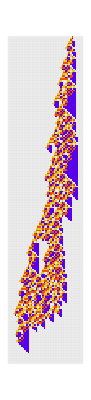
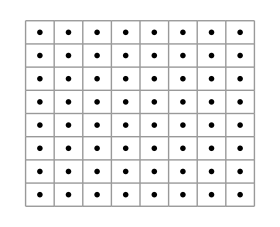

```mathematica
Row[{ArrayPlot[ArrayPad[CellularAutomaton[{109119604060725664814308901024268869132,4,1},{{1},0},200],{{0,0},{3,3}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.05]],RulePlot[CellularAutomaton[{109119604060725664814308901024268869132,4,1}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]][[1,1,All,All,1]]//Flatten//Partition[#,UpTo[8]]&//GraphicsGrid[#,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]&},Spacer[20]]
```

But this isn’t just a random cellular automaton. We reached this pattern through an “evolution”, where we started from the null rule and repeatedly made random, single-bit changes (mutations) to the ruleset only keeping the changes that lead to a longer or equal finite length, here we show only the changes to the rules that we kept:

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
evo = Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+181];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
];
```

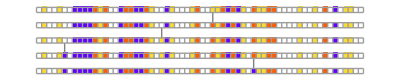
-Graphics-
⋮
-Graphics-
⋮

```mathematica
Column[{{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[evo][[1;;5,1]],"Arrows"->"Line",ImageSize->400],"⋮",{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[evo][[100;;104,1]],"Arrows"->"Line",ImageSize->400],"⋮"},Center]
```

And here we show the steps of the evolution where a longer pattern was discovered:

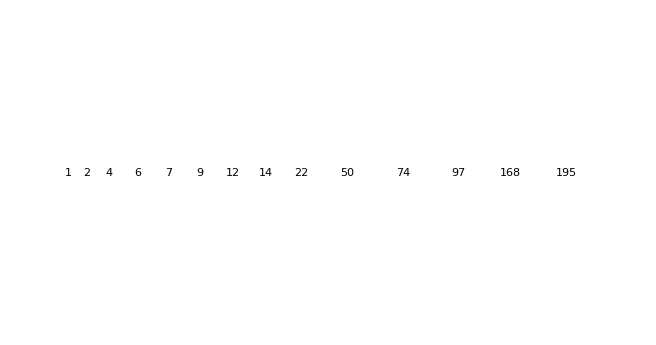

```mathematica
GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[First[#],"Trim"->{1,5},ImageSize->{Automatic,22.5 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@Rest[evo[[ResourceFunction["ProgressiveMaxPositions"][evo[[All, -1]]]]]]]
```

So the “goal” of our organisms is to “live” as many steps as possible and then terminate. And the rules determine how the organism achieves this goal.

The similarities are already striking between this and biological evolution. We can see how the pattern builds on the ideas of its predecessors, for example the above automaton contains purple triangles throughout its history.

Zooming out, we can run multiple evolutions and see different potential evolutionary paths:

```mathematica
evos = 
Table[Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+i];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
], {i,{41, 43, 105}}] ;
```

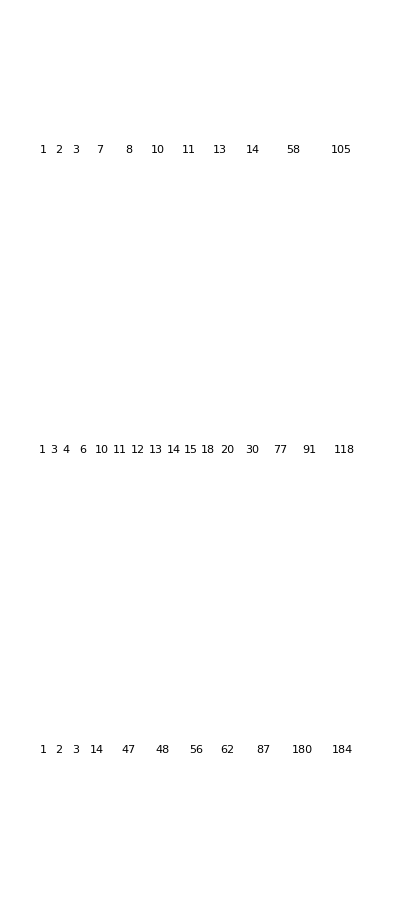

```mathematica
Column[MapThread[Function[{evo, steps}, GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[First[#],"Trim"->{1,5},ImageSize->{Automatic,22.5 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(Rest[evo[[ResourceFunction["ProgressiveMaxPositions"][evo[[All, -1]]]]]])]], {evos, {105, 120, 190}}],Spacer[1]]
```

And this gives us a powerful analogy to the discrete categories of organisms in the form of species that we observe in biology, and where the variation between them comes from.

### Primitive structure

But what about the nature of the actual patterns? How do these automata achieve their goal? Well, one feature that jumps out is the apparent randomness of the patterns. It’s not clear why the patterns end up terminating at the step they do. Looking closely at one of our evolved automata, we can readily see that trying to figure out why it works is like trying to jump ahead of a computational irreducible process:

```mathematica
rob = ;
reg = ;
(*See biomedicine-04 for definition*)
```

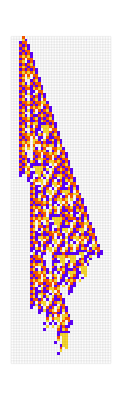

```mathematica
ArrayPlot[ArrayPad[CellularAutomaton[reg[[43, 1]],{{1},0},120],{{0,0},{3,3}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.05]]
```

But just how random are these automata, and is their any regularity or structure we can find among them? 
To answer this, we can look at a random sample of the rule space:

```mathematica
SeedRandom[5555];
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[{FromDigits[#, 4], 4, 1}, {{1}, 0}, {200, {-200, 200}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {15 , 4^(2*1+1) - 1}]), 3], ImageSize->{600, Automatic}]
```

-Graphics-

And compare that with a random sample of our evolved automata:

```mathematica
rob = ;
reg = ;
(*See biomedicine-04 for definition*)
```

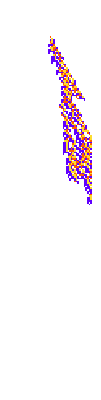

```mathematica
SeedRandom[6666];
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[#,{{1}, 0}, {200, {-25, 25}}], ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]]& /@RandomSample[reg[[All, 1]], 16], 8]]
```

What becomes obvious here is that because the automata are required to terminate, we have selected for “skinnier” patterns, with slower “growth-rates” as measured by the width of the colored cell range at each step. Here is a comparison between the growth rates for the random vs. evolved:

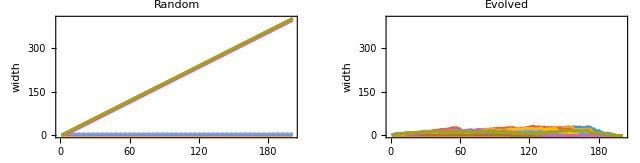

```mathematica
SeedRandom[6666];
GraphicsRow[{
ListLinePlot[If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@CellularAutomaton[{FromDigits[#, 4], 4, 1},{{1}, 0}, 200]&/@(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {10 , 4^(2*1+1) - 1}]), PlotHighlighting->None,  Frame->True, AspectRatio->.4, FrameLabel->{"steps", "width"}, PlotLabel->"Random"],
ListLinePlot[If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@CellularAutomaton[#,{{1}, 0}, 200]&/@RandomSample[reg[[All, 1]], 10], PlotRange->400, Filling->Bottom, PlotHighlighting->None, Frame->True, AspectRatio->.4, FrameLabel->{"steps", "width"}, PlotLabel->"Evolved"]

}]
```

So clearly the evolved patterns are not completely random in their construction. And we can think of this as the beginnings of structure in our computational biological universe, where the fitness landscape pushes organisms away from complete randomness, into specific niches in order to solve a particular problem.

So this is an example of the formation of high-level structure. But what about at the level of the rules? Can we find any regularities there?

To do this, we can look at the frequencies of various colors for all the possible rules in the random and evolved groups:

```mathematica
Column[MapThread[Function[{digs,label}, With[{aps = Rasterize[ArrayPlot[List/@#,ImageSize->{10, 25}, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"](*, Mesh->True, MeshStyle->Opacity[.4]*)]]& /@ RuleTuples[4, 1]}, BarChart[BinCounts[#, {0, 4, 1}]&/@Transpose[digs], ChartLayout->"Stacked", ChartBaseStyle->EdgeForm[Thickness[.1]], ChartStyle->(Directive[EdgeForm[Directive[Opacity[1], Gray]], #]&)/@ {{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]], ChartLabels->{aps, None}, LabelingSize->35, AspectRatio->.4, ImageSize->{600, Automatic}, Frame->True, FrameLabel->{"rule", "counts"},PlotLabel->label]]],
{{(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {200 , 4^(2*1+1) - 1}]),Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)]]&/@ reg[[All, 1]]}, {"Random", "Evolved"}}]]
```

-Graphics-

So on the y-axis here we have the counts of the different output colors for each rule. As you’d expect, the random group basically has an equal distribution of the different output colors for each rule. But with the evolved group, we can see that certain rules have an unequal distribution, and in particular, keeping in mind our growth inhibition plots, we can notice that the rules with two white-cells on the edge always have a higher probability of outputting a white cell. These rules, occur on the borders of the pattern, and therefore are important for determining the growth rate of the pattern. Here we show these “edge-rules” highlighted in red:

```mathematica
SeedRandom[6666];

GraphicsRow[Function[ca, 
Module[{b = Array[0 &, {Length[ca], Length[ca[[1]]]}]}, 
gray = ReplacePart[b, Thread[bodyidxs[ca]-> 1]];
redidxs = 
MapIndexed[Function[{val, idx}, {idx[[1]], #}&/@ val], DeleteCases[(Flatten/@Function[row, If[# === {}, {}, Range@@@#]&[SequencePosition[row, #]]&/@ edgerules]/@ca), {}]];
ArrayPlot[ReplacePart[gray, Thread[redidxs->2]], ColorRules->{0->White, 1->LightGray, 2->Red}]
]]/@ (CellularAutomaton[#, {{1}, 0}, 200]&/@RandomSample[reg[[All, 1]], 10])]
```

-Graphics-

So interestingly, what we’re seeing here is the development of a low-level mechanism within our automata, that helps the “organism” achieve its goal. In biological terms, this is analogous to a particular gene being selected for because it say, inhibits unhealthy growth.

### Squeezing irreducibility out of the system

Okay, so we’ve identified some regularity and structure at multiple scales within this evolved group, but there is still plenty of irreducibility within these systems. For example, the “growth patterns” within the “body” of the automaton still look very random, and the details of why they grow and why they stop growing are very complicated. And this is reflected in the frequencies of the “inner-rules”, which from the plot above we can see look very much like the random group.

So how can we push our automata further away from this irreducibility? Well, one difference between our evolution here and real evolution, is that organisms in biology have to be able to achieve their goal even when the details of the environment change. For example, the exact locations of the cells within a frog embryo may change, but it still needs to be able to grow into a tadpole and then a frog.

In the evolution we ran previously, the “environment” is always a blank slate of white cells. You may imagine, that forcing our automata to achieve their goal in multiple different environments could lead to more purposeful mechanisms within the system.

To test this, we can run an evolution very similar to our first one, but instead of running the rules only in an all-white environment at each step, we can run them in multiple environments, each differing by a single cell. So here is an example step in one of our “perturbed evolutions”, with an arrow pointing to the cell that was changed:

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
SeedRandom[426778+132];
perts = Reap[bye = NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
(*pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];*)
pcas = Table[PerturbedCellularAutomaton[ru,{{1}, 0},{200, {-200, 200}}],5];
Sow[{ru, pcas[[All, 2]]}];
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},2000]][[2, 1]];
```

```mathematica
kept = Select[perts, MemberQ[bye[[All, 1]],#[[1]]]&] ;
```

```mathematica
GraphicsRow[Function[{ru, perts}, With[{ca = PerturbedCellularAutomaton[ru, {{1}, 0}, {28,  {-200, 200}}, #]},Labeled[PlotCA[ca, Mesh->True],Text[ TestCALifeTime[ca]]]]&/@ Prepend[perts, <||>]]@@kept[[104]]]
```

-Graphics-

And we now define our fitness as the minimum length of all the resulting patterns (including the unperturbed one). So in the above case the fitness would be fifteen. One important note is that if any of the patterns go past the cutoff length (we used two-hundred in the evolution below) then the fitness is zero. So this case for example would have a fitness of zero:

```mathematica
GraphicsRow[Function[{ru, perts}, With[{ca = PerturbedCellularAutomaton[ru, {{1}, 0}, {200,  {-200, 200}}, #]},Labeled[PlotCA[ca],Text[ TestCALifeTime[ca]]]]&/@ Prepend[perts, <||>]]@@perts[[750]]]
```

-Graphics-

And because of that, we are putting pressure on the system to avoid “blowing up”, and we’ll see later how it adapts to this challenge.

So what is the result from our robust evolution? Here are the resulting lifetimes from a regular and a perturbed evolution:

```mathematica
Column[MapThread[Function[{idxs, labs}, 
ListPlot[MapIndexed[
Module[{ca = CellularAutomaton[#, {{1}, 0}, 200], lt},
lt = TestCALifeTime[ca];
If[MemberQ[r, #2[[1]]],Callout[lt, PlotCA[ArrayPad[#, 1]&/@ca,"Trim"->{None, 5}, ImageSize->{Automatic,25 Sqrt[1+lt]}], LabelVisibility->All], TestCALifeTime[ca]]]&, idxs], LabelingSize->75, Filling->Bottom, AspectRatio->.4, ImageSize->{600, Automatic}, PlotRange->{{0, 200}, {0, 250}}, PlotLabel->labs, Frame->True, FrameLabel->{"pattern", "lifetime"}]], {{reg[[sireg, 1]], rob[[sortedidxs, 1]]}, {"Regular Evolution", "Perturbed Evolution"}}]]
```

-Graphics-
-Graphics-

So first off, the length of the automata in the perturbed evolution are quite a bit shorter, which makes sense because, as we mentioned above, any perturbed pattern that runs past the cut-off length will cause the whole group’s fitness to be zero. So it gets harder and harder to increase the length of the automaton as you approach the end-line. But, despite this, a few of our patterns have managed to still live quite long, here is the top ten longest lived patterns from our perturbed evolution:

```mathematica
With[{cas = CellularAutomaton[#, {{1}, 0}, {200}]&/@ rob[[All, 1]]},
GraphicsRow[
Labeled[PlotCA[ArrayPad[#, 1]&/@#, Frame->True], TestCALifeTime[#]]&/@TakeLargestBy[cas, TestCALifeTime, 10], ImageSize->{600, Automatic}]
]
```

-Graphics-

But we don’t just care about the lifetime, we also want to see the lifetime under perturbation. Here we show the automata with the highest mean lifetime under perturbation, along with their respective lifetime distributions:

```mathematica
l1 = Select[rob, TestCALifeTime[CellularAutomaton[#[[1]], {{1}, 0}, 200]]>100&];
```

```mathematica
samplts = ParallelMap[Table[TestCALifeTime[{{"[◼]", "PerturbedCellularAutomaton"}}[#,{{1},0},{200,{-100,100}}]], 200]&,l1[[All, 1]]];
```

```mathematica
Iconize[samplts]
```

```mathematica
samplts = ;
```

```mathematica
zd = (samplts /. -Infinity->0);
```

```mathematica
bmi = With[{zd = (samplts /. -Infinity->0)}, 
ReverseSortBy[Range[Length[l1]],Mean[zd[[#]]]&]];
```

```mathematica
means = N[Mean/@ zd];
```

```mathematica
GraphicsGrid[Partition[MapIndexed[BarChart[ReplacePart[#,10->Callout[#[[10]], PlotCA[l1[[bmi[[#2[[1]]]], 1]], "Trim"->{1, 3}], Above, Appearance->None]] ,PlotRange->100,Frame->True, FrameTicks->{{If[#2[[1]] == 1 || #2[[1]] == 4, Automatic, None],Automatic}, {If[4 <=#2[[1]] <= 6,  Table[{i, 5i}, {i, 0,50, 10}], None], Automatic}}, BarSpacing->None,ImageSize->{If[#2[[1]] == 1 || #2[[1]] == 4,285, 280], Automatic} , LabelingSize->100, PlotRange->150, PlotRangePadding->{Automatic, 0},
Epilog->{Dotted, Red, Line[{{means[[bmi[[#2[[1]]]]]]/5, 100}, {means[[bmi[[#2[[1]]]]]]/5, 0}}]}
]&, 
MapAt[Style[#,Red]&, BinCounts[#, {5}]&/@(samplts[[bmi[[;;6]]]]/.-Infinity->210), {All, -1}]], 3], Spacings->0, ImageSize->{600, Automatic}]
```

-Graphics-

So the big yellow automaton, is far more robust than the others. Why is this? Looking at some sample perturbations, we can see that many of the changes have little effect on the pattern.

```mathematica
GraphicsRow[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}, #] ,"ArrowSize"->Small]&/@{<||>,<|{89,201}->1|>,<|{82,206}->2|>,<|{135,215}->1|>,<|{105,213}->2|>,<|{22,199}->0|>,<|{40,202}->0|>,<|{64,197}->2|>, <|{83,215}->0|>}]
```

-Graphics-

Running the rule from various random initial conditions we can see it is an attractor, meaning that it results in a similar shape despite changes in the initial state:

```mathematica
GraphicsRow[Table[PlotCA[CellularAutomaton[l1[[bmi[[1]], 1]], {RandomChoice[{0, 1, 2, 3}, 30], 0}, 250]], 5]]
```

-Graphics-

But, it does not just attract directly to white, instead it attracts to the yellow blade, which is a simple pattern, that reliably achieves the goal of living some long number of finite steps. And if we perturb the yellow blade itself, the automaton still has achieves this goal:

```mathematica
SeedRandom[8888];
GraphicsRow[Prepend[Table[PlotCA[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {200, {-200, 200}}, {RandomChoice[#[[80;;120]]]&,RandomChoice[#[[210;;220]]]& }]], 5], PlotCA[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {200, {-200, 200}}, {}]]]]
```

-Graphics-

So in a way, this pattern is solving the given problem in a much more “purposeful” way, in contrast to the patterns observed in the regular evolution.

To get a better sense of this, we can look at a sensitivity plot of all possible perturbations to this automaton, with each cell indicating the degree to which changing that cell affects the lifetime:

```mathematica
lts = With[{aps = allperts[l1[[bmi[[1]], 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
Iconize[lts]
```

```mathematica
rel = Abs[190  - #]&/@(lts/.-Infinity->401);
```

```mathematica
byidx = Partition[rel, 3];
```

```mathematica
blt = Mean/@byidx;
```

```mathematica
GraphicsRow[Reverse@{
Module[{ca = CellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, 200], lt},
lt = TestCALifeTime[ca];
ArrayPlot[
ReplacePart[Array[-1&, Dimensions[ca]], Thread[Catenate[bodyidxs[ca]]->blt]] ,ColorFunctionScaling->False,ColorFunction->(If[#==-1,White, Blend[{LightYellow, Yellow,  Orange, Red}, # / lt]]&)]],
PlotCA[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {200, {-200, 200}}, {}], MeshStyle->Opacity[.1]]}]
```

-Graphics-

So clearly, the yellow blade is performing a specific function, which is to live long and be robust. For comparison, here are some automata from the regular evolution:

```mathematica
lts2 = With[{aps = allperts[reg[[43, 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[reg[[43, 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
Iconize[lts2]
```

```mathematica
lts3 = With[{aps = allperts[reg[[181, 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[reg[[181, 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
Iconize[lts3]
```

```mathematica
lts4 = With[{aps = allperts[reg[[41, 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[reg[[41, 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
Iconize[lts4]
```

```mathematica
GraphicsRow[MapThread[Function[{rule, lts}, 
Module[{cal,ca, lt, byidx, blt},
cal =ArrayPad[#, 1]&/@ CellularAutomaton[rule, {{1}, 0}, 400];
lt = TestCALifeTime[cal];
ca = CellularAutomaton[rule, {{1}, 0}, lt + 5];
rel = Abs[lt  - #]&/@(lts/.-Infinity->401);
byidx = Partition[rel, 3];
blt = Mean/@byidx;
GraphicsRow[{
PlotCA[ca],
ArrayPlot[
ReplacePart[Array[-1&, Dimensions[ca]], Thread[Catenate[bodyidxs[ca]]->blt]] ,ColorFunctionScaling->False,ColorFunction->(If[#==-1,White, Blend[{LightYellow, Yellow,  Orange, Red}, # / lt]]&)]
}]
]],{{ reg[[43, 1]],reg[[181, 1]], reg[[41, 1]]}, {lts2, lts3, lts4}}]]
```

-Graphics-

So these automata are not nearly robust, and also there is no predictable pattern to how they react to perturbations. Looking at our other robust automata from the perturbed evolution now, we can see that they are less fragile than the regular ones, but have no clear mechanism for their robustness, which limits their ability to have a long perturbed lifetime:

```mathematica
roblts =  
Function[rule, 
With[{aps = allperts[rule, {{1}, 0}, {400, {-100, 100}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[rule, {{1}, 0}, {400, {-100, 100}}, #]]&, aps]]]/@ l1[[bmi[[2;;6]], 1]];
```

```mathematica
Iconize[roblts]
```

```mathematica
GraphicsRow[MapThread[Function[{rule, lts}, 
Module[{cal,ca, lt, byidx, blt},
cal =ArrayPad[#, 1]&/@ CellularAutomaton[rule, {{1}, 0}, 400];
lt = TestCALifeTime[cal];
ca = CellularAutomaton[rule, {{1}, 0}, lt + 5];
rel = Abs[lt  - #]&/@(lts/.-Infinity->401);
byidx = Partition[rel, 3];
blt = Mean/@byidx;
(*GraphicsRow[{
PlotCA[ca],*)
ArrayPlot[
ReplacePart[Array[-1&, Dimensions[ca]], Thread[Catenate[bodyidxs[ca]]->blt]] ,ColorFunctionScaling->False,ColorFunction->(If[#==-1,White, Blend[{LightYellow, Yellow,  Orange, Red}, # / lt]]&)]
(*}]*)
]],{l1[[bmi[[2;;6]], 1]], roblts}]]
```

-Graphics-

So what is going on here, why exactly did we incentivize more structure in the perturbed evolution?

Well, at a high level, we can think of our regular evolution as trying to find a program that takes a single “seed” state and results in a long-lived pattern. And we can think of our perturbed evolution as trying to find a program that goes from a set of different states and results in a long-lived pattern.

And the point is that because, in the perturbed evolution, the task the program has to solve is more “challenging” or “general”, the resulting programs will necessarily be less random or more “structured”, as we’re observing in the case of this big yellow automaton.

And in fact, this is a fairly robust result, running many perturbed evolutions we see that the rules that have the longest lifetimes under perturbation, also tend to have more structure, here are some examples:

```mathematica
rrs = [[{1, 2, 4, 5, 6, 7, 8, 9, 10, 11, 14, 15, 16, 19}]];
```

```mathematica
GraphicsGrid[Partition[{{"[◼]", "PlotCA"}}[CellularAutomaton[First[#],{{1},0},{150,{-100,100}}],ImageSize->{Automatic,400}]&/@Delete[rrs,List/@{3,6}], 6]]
```

-Graphics-

And looking at the sensitivity plot of these rules, we can see that indeed, they do often have similarly “explainable” mechanisms:

```mathematica
rrs = [[{1, 2, 4, 5, 6, 7, 8, 9, 10, 11, 14, 15, 16, 19}]];
```

```mathematica
structlts =  
Function[rule, 
With[{aps = allperts[rule, {{1}, 0}, {400, {-100, 100}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[rule, {{1}, 0}, {400, {-100, 100}}, #]]&, aps]]]/@ rrs[[All, 1]];
```

```mathematica
Iconize[structlts]
```

```mathematica
GraphicsGrid[Partition[MapThread[Function[{rule, lts}, 
Module[{cal,ca, lt, byidx, blt},
cal =ArrayPad[#, 1]&/@ CellularAutomaton[rule, {{1}, 0}, 400];
lt = TestCALifeTime[cal];
ca = CellularAutomaton[rule, {{1}, 0}, lt + 5];
rel = Abs[lt  - #]&/@(lts/.-Infinity->401);
byidx = Partition[rel, 3];
blt = Mean/@byidx;
ArrayPlot[
ReplacePart[Array[-1&, Dimensions[ca]], Thread[Catenate[bodyidxs[ca]]->blt]] ,ColorFunctionScaling->False,ColorFunction->(If[#==-1,White, Blend[{LightYellow, Yellow,  Orange, Red}, # / lt]]&),ImageSize->{Automatic,325}]
(*}]*)
]],{Delete[rrs[[All,1]],List/@{3,6}], Delete[structlts,List/@{3,6}]}], 6]]
```

-Graphics-

So it seems that we’ve touched on a general feature of the nature of adaptive systems, which is that as we increase the noise in the environment, or the “generality” of the task, we also increase the resulting structure within the system.

But one could ask, given that we’ve found some pocket of reducibility in the pattern, will we also see reducibility at the level of the rules? In other words, is it structure all the way down?

One way to see this, is to look at the causal rule graph, where each node is a rule, and each edge represents any time one rule lead to another, with the thickness of the edge corresponding to the frequency of the “pathway”. We can think of this as our gene network, and much like in real biology, it’s a complete mess:

```mathematica
subs = getsubs[l1[[bmi[[1]], 1]]];
```

```mathematica
nextrus[rus_]:= 
Partition[ArrayPad[Replace[#, subs]&/@ rus, 1, 0], 3, 1]
```

```mathematica
init = CenterArray[1, 50];
```

```mathematica
tab = NestList[nextrus, Partition[init, 3, 1],200];
```

```mathematica
With[{ws =KeyDrop[Counts[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]]], {({0, 0, 0}->{0, 0, 0})}]},  Graph[KeyValueMap[Style[#1, Thickness[.001#2^.5]]&, ws], VertexShapeFunction->(Inset[ArrayPlot[{#2}, ImageSize->30, ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]], #1]&), EdgeWeight->Values[ws], GraphLayout->"SpringElectricalEmbedding"]]
```

-Graphics-

If we look at this graph only only within the blade section:

```mathematica
bt = tab[[100;;200, ;;25]];
```

```mathematica
Length[tab]
```

201

```mathematica
PlotCA[Join[#[[1]], #[[2;;,-1]]]&/@ tab]
```

-Graphics-

```mathematica
Dimensions[bt]
```

{101,25,3}

```mathematica
With[{ws =KeyDrop[Counts[Flatten[Table[bt[[i, j]]->bt[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[bt[[1]]]&], {i,1, Length[bt] - 1}, {j, 1, Length[bt[[1]]]}]]], {({0, 0, 0}->{0, 0, 0})}]},  Graph[KeyValueMap[Style[#1, Thickness[.001#2]]&, ws], VertexShapeFunction->(Inset[ArrayPlot[{#2}, ImageSize->30, ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]], #1]&), EdgeWeight->Values[ws], GraphLayout->"SpringElectricalEmbedding"]]
```

-Graphics-

Other than the fact that yellow seems to

And a

We can look at for example

So okay, we are beginning to understand when and where we should expect to see structure in the computational biological universe. But the big question is, given that we find some explainable mechanisms can we take advantage of this reducibility and predictably influence the behavior of the system. This, in a way, is the fundamental question behind the fields of medicine and human performance,

And interestingly, we can see this in real biological systems as well. One example is morphogenesis in different animals.

Planaria for example, reproduce by ripping themselves in half (one side is the head and one is the tail) and then have each side regrow the missing half. What that means, is that the actual tissue of planaria can in principle be millions of years old. Therefore, the individual cells in the organism are quite unreliable. And in fact, if you look at the genome of a planaria cell, it is a mess, with extra chromosomes and errors all over the place, something you’d expect to see in cancer cells in mammals.

And because of this unreliability, the mechanisms for growth and movement of cell tissue, have to be very purposeful and structured, much in the same way our yellow automaton found a deliberate mechanism for “absorbing” errors.

In contrast, mammals like humans, develop from a single cell, so you get “brand new” tissue. And this means that the parts are more reliable and therefore the mechanisms for doing morphogenesis don’t have to be so structured and purposeful, and are much more irreducible. In a sense, morphogenesis in mammals is much more like our first evolution, where we are looking for a “one-to-one” function. And morphogenesis in something like planaria, is much more like our perturbed evolution where we are looking for an “all-to-one” function.

And it has been shown that we can actually predictably influence the morphogenesis of planaria . For instance, we can perturb the system in such a way that it grows two heads, instead of a head and a tail . Understanding and controlling the behavior of the structure within an adaptive system is something that Stephen Wolfram and I explored in depth in our recent post on biomedicine, and is something I will come back to .

And that brings us to the question